Aprendizaje automático

Hasta este punto en el libro, cuando se ha querido indicar a Wolfram Language que se desea hacer alguna cosa, hay que escribir código para decirle exactamente lo que tiene que hacer. Sin embargo, Wolfram Language tiene la capacidad de aprender lo que tiene que hacer refiriéndose a ejemplos, utilizando la idea del aprendizaje de máquinas.

Aquí se explicará cómo puede entrenarse al lenguaje para hacer eso. Pero se verán primero algunas funciones nativas que ya han sido entrenadas con un gran número de ejemplos.

LanguageIdentify toma porciones de texto e identifica el lenguaje humano en que está escrito.

Identifique en qué lengua está escrita cada frase:

```mathematica
LanguageIdentify[{ "thank you","merci","dar las gracias","感謝","благодарить"}]
```

{English,French,Spanish,Chinese,Russian}

Wolfram Language puede también realizar tareas considerablemente más difíciles, de “inteligencia artificial”, tales como la identificación de imágenes.

Identifique de qué es una imagen:

```mathematica
ImageIdentify[-Graphics-]
```

cheetah

Existe una función general, Classify, a la que se le han enseñado varios tipos de clasificación. Por ejemplo, clasificar el “sentimiento” de un texto.

Un texto optimista se clasifica como de sentimiento positivo:

```mathematica
Classify["Sentiment","I'm so excited to be programming"]
```

Positive

Un texto pesimista se clasifica como de sentimiento negativo:

```mathematica
Classify["Sentiment","math can be really hard"]
```

Negative

Uno mismo puede llevar a cabo el entrenamiento de Classify. Un ejemplo sencillo es la clasificación de dígitos manuscritos como 0 o 1. Se le da a Classify una colección de ejemplos de entrenamiento, seguidos por un dígito particular escrito a mano. La respuesta será 0 o 1 para ese dígito manuscrito.

Con ejemplos de entrenamiento, Classify identifica correctamente un 0 escrito a mano:

```mathematica
Classify[{-Graphics-->0,-Graphics-->1,-Graphics-->0,-Graphics-->1,-Graphics-->1,-Graphics-->0,-Graphics-->0,-Graphics-->1,-Graphics-->1,-Graphics-->0,-Graphics-->0,-Graphics-->0,-Graphics-->1,-Graphics-->0,-Graphics-->1,-Graphics-->0,-Graphics-->1,-Graphics-->1,-Graphics-->1},
-Graphics-]
```

0

Para darse una idea de cómo trabaja lo anterior, y porque es útil por sí mismo, se describirá la función Nearest, que encuentra cuál de los elementos de una lista es el más próximo al que uno le dé.

Encuentre cuál de los elementos de la lista es el más próximo a 22:

```mathematica
Nearest[{10,20,30,40,50,60,70,80},22]
```

{20}

Encuentre los tres números más próximos:

```mathematica
Nearest[{10,20,30,40,50,60,70,80},22,3]
```

{20,30,10}

Nearest también puede encontrar los colores más próximos.

En la lista que sigue, encontrar los 3 colores que estén más próximos al que se da:

```mathematica
Nearest[{Hue[0.],Hue[0.05],Hue[0.1],Hue[0.15000000000000002],Hue[0.2],Hue[0.25],Hue[0.30000000000000004],Hue[0.35000000000000003],Hue[0.4],Hue[0.45],Hue[0.5],Hue[0.55],Hue[0.6000000000000001],Hue[0.65],Hue[0.7000000000000001],Hue[0.75],Hue[0.8]},RGBColor[0.8727094319714808, 0.9066617343162084, 0.09569669807641734],3]
```

{Hue[0.15000000000000002],Hue[0.2],Hue[0.25]}

También funciona con palabras.

Encuentre las 10 palabras más próximas a “good” en la lista de palabras:

```mathematica
Nearest[WordList[ ],"good",10]
```

{good,food,goad,god,gold,goo,goody,goof,goon,goop}

También existe la noción de cercanía para imágenes. Y, aunque dista de ser todo lo que hay, esto es, en efecto, parte de lo que usa ImageIdentify.

Otro asunto que también está relacionado es el reconocimiento de texto (reconocimiento óptico de caracteres u OCR). Se toma una porción de texto para hacerla borrosa.

Cree una imagen de la palabra “hello”, y hágala borrosa:

```mathematica
Blur[Rasterize[Style["hello",30]],3]
```

-Graphics-

TextRecognize tiene la capacidad de reconocer el texto original a partir de uno borroso.

Reconozca el texto en la imagen:

```mathematica
TextRecognize[-Graphics-]
```

hello

Si el texto está demasiado borroso,TextRecognize no podrá reconocer lo que dice, aunque probablemente una persona tampoco.

Genere una secuencia de porciones de texto progresivamente más borrosas:

```mathematica
Table[Blur[Rasterize[Style["hello",15]],r],{r,0,4}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

A medida que el texto se hace más borroso, TextRecognize comete errores, hasta que desiste por completo:

```mathematica
Table[TextRecognize[Blur[Rasterize[Style["hello",15]],r]],{r,0,4}]
```

{hello,hello,hella,,}

Algo similar sucede si se hace más y más borrosa la imagen de un guepardo. Mientras la imagen esté más o menos nítida, ImageIdentify la identificará correctamente como guepardo. Pero cuando es ya demasiado borrosa, ImageIdentify comienza por confundirla con un león, hasta que su mejor conjetura es que se trata de una persona.

Haga cada vez más borrosa la imagen de un guepardo:

```mathematica
Table[Blur[-Graphics-,r],{r,0,22,2}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Cuando la imagen está ya demasiado borrosa, ImageIdentify deja de suponer que es un guepardo:

```mathematica
Table[ImageIdentify[Blur[-Graphics-,r]],{r,0,22,2}]
```

{cheetah,cheetah,cheetah,cheetah,lion,red wolf,domestic dog,musteline mammal,domestic dog,person,person,person}

ImageIdentify normalmente contesta lo que supone es la identificación más verosímil. Sin embargo, se le puede dar una lista de identificaciones posibles, comenzando por la más verosímil. Aquí aparecen las 10 identificaciones posibles más verosímiles, en todas las categorías, comenzando por la primera.

ImageIdentify supone que esto podría ser un guepardo, pero es más verosímil que sea un león o hasta un perro:

```mathematica
ImageIdentify[-Graphics-,All,10]
```

{lion,red wolf,cheetah,wildcat,domestic dog,striped hyena,pine marten,mountain lion,working dog,lynx}

Cuando la imagen está suficientemente borrosa, ImageIdentify puede hacer suposiciones a lo loco sobre lo que puede ser:

```mathematica
ImageIdentify[-Graphics-,All,10]
```

{person,domestic dog,edible fruit,hunting dog,cat,berry,terrier,wildcat,working dog,soft-finned fish}

En el aprendizaje de máquinas se suele dar el entrenamiento explícitamente, por ejemplo, diciendo “esto es un guepardo”, “esto es un león”. Aunque a veces simplemente se desea encontrar categorías de cosas sin un entrenamiento específico previo.

Una forma de lograr lo anterior es comenzar por tomar una colección de cosas, como colores, y entonces formar cúmulos con las que sean similares. Esto puede lograrse usando FindClusters.

Forme “cúmulos” de colores similares en listas separadas:

```mathematica
FindClusters[{RGBColor[{0.048175746346922704, 0.8856231902848692, 0.002187262571789972}],RGBColor[{0.9543437880041175, 0.9364915417894851, 0.08314980598714755}],RGBColor[{0.8527294202095301, 0.15459949958575997, 0.08139444813034824}],RGBColor[{0.12965437429396431, 0.8338364200576898, 0.16859742903104202}],RGBColor[{0.14189318640501342, 0.8685451286121387, 0.10426943556314977}],RGBColor[{0.9244703510275273, 0.001783470411052479, 0.14318146272477922}],RGBColor[{0.8340523614444824, 0.038129646837010533, 0.09354464468116397}],RGBColor[{0.06423181065333894, 0.9361486399945784, 0.08411970647251821}],RGBColor[{0.8676164929883508, 0.8866580065099905, 0.024086278089002183}],RGBColor[{0.8577958146408966, 0.8374035340744639, 0.0071190816223388464}],RGBColor[{0.9967431643372854, 0.969475575859666, 0.12251095291379577}],RGBColor[{0.8543889209256321, 0.09697598692920356, 0.10750903324099509}],RGBColor[{0.8500363984900003, 0.9263311671408848, 0.13924242858059316}],RGBColor[{0.9879209034166253, 0.8377732017482453, 0.15613661869756118}],RGBColor[{0.9573167308698426, 0.1507116093826361, 0.09832234398916928}],RGBColor[{0.04278634258158939, 0.9055378427790535, 0.0003309996431954121}],RGBColor[{0.8058039405531526, 0.8318774133774354, 0.10151558699591279}],RGBColor[{0.006814389873512461, 0.9336694049188562, 0.06907220235176909}],RGBColor[{0.9450158125329948, 0.9670907305400336, 0.05040029871534907}],RGBColor[{0.9752641706478989, 0.8013981246170678, 0.10899973580393796}],RGBColor[{0.16590548598015492, 0.9015045495499641, 0.09828783196817376}],RGBColor[{0.10048980936842117, 0.9171495192304465, 0.16131399976146749}]}]
```

{{RGBColor[{0.048175746346922704, 0.8856231902848692, 0.002187262571789972}],RGBColor[{0.12965437429396431, 0.8338364200576898, 0.16859742903104202}],RGBColor[{0.14189318640501342, 0.8685451286121387, 0.10426943556314977}],RGBColor[{0.06423181065333894, 0.9361486399945784, 0.08411970647251821}],RGBColor[{0.04278634258158939, 0.9055378427790535, 0.0003309996431954121}],RGBColor[{0.006814389873512461, 0.9336694049188562, 0.06907220235176909}],RGBColor[{0.16590548598015492, 0.9015045495499641, 0.09828783196817376}],RGBColor[{0.10048980936842117, 0.9171495192304465, 0.16131399976146749}]},{RGBColor[{0.9543437880041175, 0.9364915417894851, 0.08314980598714755}],RGBColor[{0.8676164929883508, 0.8866580065099905, 0.024086278089002183}],RGBColor[{0.8577958146408966, 0.8374035340744639, 0.0071190816223388464}],RGBColor[{0.9967431643372854, 0.969475575859666, 0.12251095291379577}],RGBColor[{0.8500363984900003, 0.9263311671408848, 0.13924242858059316}],RGBColor[{0.8058039405531526, 0.8318774133774354, 0.10151558699591279}],RGBColor[{0.9450158125329948, 0.9670907305400336, 0.05040029871534907}]},{RGBColor[{0.8527294202095301, 0.15459949958575997, 0.08139444813034824}],RGBColor[{0.9244703510275273, 0.001783470411052479, 0.14318146272477922}],RGBColor[{0.8340523614444824, 0.038129646837010533, 0.09354464468116397}],RGBColor[{0.8543889209256321, 0.09697598692920356, 0.10750903324099509}],RGBColor[{0.9573167308698426, 0.1507116093826361, 0.09832234398916928}]},{RGBColor[{0.9879209034166253, 0.8377732017482453, 0.15613661869756118}],RGBColor[{0.9752641706478989, 0.8013981246170678, 0.10899973580393796}]}}

También puede obtenerse una visión diferente conectando cada color con los tres más similares en la lista y, entonces, hacer un grafo con las conexiones. En el ejemplo anterior se obtienen así tres subgrafos no conectados.

Cree un grafo de conexiones basadas en la cercanía dentro del “espacio de colores”:

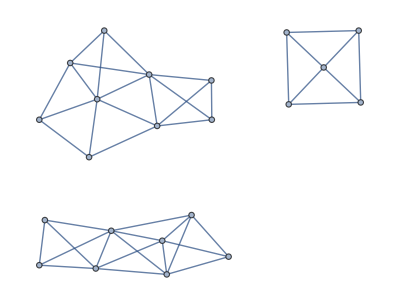

```mathematica
NearestNeighborGraph[{RGBColor[{0.048175746346922704, 0.8856231902848692, 0.002187262571789972}],RGBColor[{0.9543437880041175, 0.9364915417894851, 0.08314980598714755}],RGBColor[{0.8527294202095301, 0.15459949958575997, 0.08139444813034824}],RGBColor[{0.12965437429396431, 0.8338364200576898, 0.16859742903104202}],RGBColor[{0.14189318640501342, 0.8685451286121387, 0.10426943556314977}],RGBColor[{0.9244703510275273, 0.001783470411052479, 0.14318146272477922}],RGBColor[{0.8340523614444824, 0.038129646837010533, 0.09354464468116397}],RGBColor[{0.06423181065333894, 0.9361486399945784, 0.08411970647251821}],RGBColor[{0.8676164929883508, 0.8866580065099905, 0.024086278089002183}],RGBColor[{0.8577958146408966, 0.8374035340744639, 0.0071190816223388464}],RGBColor[{0.9967431643372854, 0.969475575859666, 0.12251095291379577}],RGBColor[{0.8543889209256321, 0.09697598692920356, 0.10750903324099509}],RGBColor[{0.8500363984900003, 0.9263311671408848, 0.13924242858059316}],RGBColor[{0.9879209034166253, 0.8377732017482453, 0.15613661869756118}],RGBColor[{0.9573167308698426, 0.1507116093826361, 0.09832234398916928}],RGBColor[{0.04278634258158939, 0.9055378427790535, 0.0003309996431954121}],RGBColor[{0.8058039405531526, 0.8318774133774354, 0.10151558699591279}],RGBColor[{0.006814389873512461, 0.9336694049188562, 0.06907220235176909}],RGBColor[{0.9450158125329948, 0.9670907305400336, 0.05040029871534907}],RGBColor[{0.9752641706478989, 0.8013981246170678, 0.10899973580393796}],RGBColor[{0.16590548598015492, 0.9015045495499641, 0.09828783196817376}],RGBColor[{0.10048980936842117, 0.9171495192304465, 0.16131399976146749}]},3,VertexLabels->All]
```

Un dendrograma es una representación gráfica tipo árbol, que permite observar una jerarquía completa de qué está cerca de qué.

Muestre los colores cercanos agrupados sucesivamente:

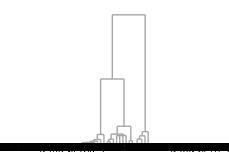

```mathematica
Dendrogram[{RGBColor[{0.048175746346922704, 0.8856231902848692, 0.002187262571789972}],RGBColor[{0.9543437880041175, 0.9364915417894851, 0.08314980598714755}],RGBColor[{0.8527294202095301, 0.15459949958575997, 0.08139444813034824}],RGBColor[{0.12965437429396431, 0.8338364200576898, 0.16859742903104202}],RGBColor[{0.14189318640501342, 0.8685451286121387, 0.10426943556314977}],RGBColor[{0.9244703510275273, 0.001783470411052479, 0.14318146272477922}],RGBColor[{0.8340523614444824, 0.038129646837010533, 0.09354464468116397}],RGBColor[{0.06423181065333894, 0.9361486399945784, 0.08411970647251821}],RGBColor[{0.8676164929883508, 0.8866580065099905, 0.024086278089002183}],RGBColor[{0.8577958146408966, 0.8374035340744639, 0.0071190816223388464}],RGBColor[{0.9967431643372854, 0.969475575859666, 0.12251095291379577}],RGBColor[{0.8543889209256321, 0.09697598692920356, 0.10750903324099509}],RGBColor[{0.8500363984900003, 0.9263311671408848, 0.13924242858059316}],RGBColor[{0.9879209034166253, 0.8377732017482453, 0.15613661869756118}],RGBColor[{0.9573167308698426, 0.1507116093826361, 0.09832234398916928}],RGBColor[{0.04278634258158939, 0.9055378427790535, 0.0003309996431954121}],RGBColor[{0.8058039405531526, 0.8318774133774354, 0.10151558699591279}],RGBColor[{0.006814389873512461, 0.9336694049188562, 0.06907220235176909}],RGBColor[{0.9450158125329948, 0.9670907305400336, 0.05040029871534907}],RGBColor[{0.9752641706478989, 0.8013981246170678, 0.10899973580393796}],RGBColor[{0.16590548598015492, 0.9015045495499641, 0.09828783196817376}],RGBColor[{0.10048980936842117, 0.9171495192304465, 0.16131399976146749}]}]
```

Al comparar cosas, ya sean colores o fotos de animales, puede pensarse en identificar aquellas características que permitan distinguir unas de otras. En el caso de colores, una característica podría ser qué el grado de claridad del color, o el grado de rojo que contiene. Si se trata de fotos de animales, una característica podría ser qué tan peludo se ve el animal, o cuán puntiagudas tiene sus orejas.

En Wolfram Language, FeatureSpacePlot toma colecciones de objetos y trata de encontrar cuáles serían sus “mejores” características distintivas y, entonces, usar sus valores para posicionar los objetos dentro de una gráfica.

FeatureSpacePlot no informa explícitamente sobre cuáles son las características que usa. De hecho, por lo general, son bastante difíciles de describir. Pero, a fin de cuentas, lo que sucede es que FeatureSpacePlot acomoda las cosas de modo tal que los objetos que tienen características similares quedan cerca unos de otros.

FeatureSpacePlot acomoda los colores similares en posiciones cercanas:

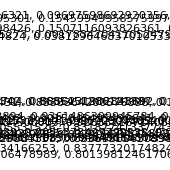

```mathematica
FeatureSpacePlot[{RGBColor[{0.048175746346922704, 0.8856231902848692, 0.002187262571789972}],RGBColor[{0.9543437880041175, 0.9364915417894851, 0.08314980598714755}],RGBColor[{0.8527294202095301, 0.15459949958575997, 0.08139444813034824}],RGBColor[{0.12965437429396431, 0.8338364200576898, 0.16859742903104202}],RGBColor[{0.14189318640501342, 0.8685451286121387, 0.10426943556314977}],RGBColor[{0.9244703510275273, 0.001783470411052479, 0.14318146272477922}],RGBColor[{0.8340523614444824, 0.038129646837010533, 0.09354464468116397}],RGBColor[{0.06423181065333894, 0.9361486399945784, 0.08411970647251821}],RGBColor[{0.8676164929883508, 0.8866580065099905, 0.024086278089002183}],RGBColor[{0.8577958146408966, 0.8374035340744639, 0.0071190816223388464}],RGBColor[{0.9967431643372854, 0.969475575859666, 0.12251095291379577}],RGBColor[{0.8543889209256321, 0.09697598692920356, 0.10750903324099509}],RGBColor[{0.8500363984900003, 0.9263311671408848, 0.13924242858059316}],RGBColor[{0.9879209034166253, 0.8377732017482453, 0.15613661869756118}],RGBColor[{0.9573167308698426, 0.1507116093826361, 0.09832234398916928}],RGBColor[{0.04278634258158939, 0.9055378427790535, 0.0003309996431954121}],RGBColor[{0.8058039405531526, 0.8318774133774354, 0.10151558699591279}],RGBColor[{0.006814389873512461, 0.9336694049188562, 0.06907220235176909}],RGBColor[{0.9450158125329948, 0.9670907305400336, 0.05040029871534907}],RGBColor[{0.9752641706478989, 0.8013981246170678, 0.10899973580393796}],RGBColor[{0.16590548598015492, 0.9015045495499641, 0.09828783196817376}],RGBColor[{0.10048980936842117, 0.9171495192304465, 0.16131399976146749}]}]
```

Por ejemplo, si se usan100 colores tomados completamente al azar, entonces FeatureSpacePlot colocará juntos aquellos que considere similares.

100 colores aleatorios acomodados mediante FeatureSpacePlot:

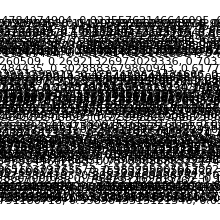

```mathematica
FeatureSpacePlot[RandomColor[100]]
```

Ahora se hará el mismo tipo de tratamiento con imágenes de letras.

Forme la imagen rasterizada de cada una de las letras del alfabeto (en inglés):

```mathematica
Table[Rasterize[FromLetterNumber[n]],{n,26}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

FeatureSpacePlot utilizará las características visuales de estas imágenes para disponerlas gráficamente. El resultado es que aquellas letras con imágenes similares, como y, v, o e, c, terminarán quedando próximas entre ellas.

```mathematica
FeatureSpacePlot[Table[Rasterize[FromLetterNumber[n]],{n,26}]]
```

-Graphics-

Aquí se hace lo mismo, pero esta vez con fotos de gatos, coches y sillas. FeatureSpacePlot separa inmediatamente los diferentes tipos de cosas.

FeatureSpacePlot coloca claramente separadas las fotos de cosas de diferentes clases:

```mathematica
FeatureSpacePlot[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

-Graphics-

Vocabulario

LanguageIdentify[texto] |   | identifica en qué lengua humana está el texto 
ImageIdentify[imagen] |   | identifica de qué es la imagen
TextRecognize[texto] |   | reconoce el texto a partir de una imagen (OCR) 
Classify[entrenamiento,datos] |   | clasifica datos a partir de entrenamiento con ejemplos 
Nearest[lista,ítem] |   | encuentra cuál elemento de lista es el más próximo a ítem 
FindClusters[lista] |   | encuentra cúmulos de elementos similares 
NearestNeighborGraph[lista,n] |   | conecta elementos de lista con sus n vecinos más cercanos 
Dendrogram[lista] |   | hace un árbol jerárquico de relaciones entre elementos
FeatureSpacePlot[lista] |   | grafica los elementos de lista en un “espacio de características”

"16 Exercises Available"
"with 7 extras" | "Get Started »"

Identifique de qué lengua procede la palabra “ajatella” . »

| Expected output: |  
  | "Finnish" |

Aplique ImageIdentify a la imagen de un tigre, donde la imagen se obtiene usando ctrl=. »

| Expected output: |  
  | "tiger" |

Forme una tabla de identificaciones de la imagen de un tigre, con borrosidades del 1 al 5. »

| Expected output: |  
  | {"tiger","tiger","domestic cat","domestic cat","person"} |

Clasifique el sentimiento de “I’m so happy to be here”. »

| Expected output: |  
  | "Positive" |

Encuentre las 10 palabras en WordList[ ] más cercanas a “happy”. »

| Expected output: |  
  | {"happy","haply","harpy","nappy","sappy","apply","campy","choppy","guppy","hairy"} |

Genere 20 números aleatorios entre 0 y 1000, y encontrar los 3 que estén más próximos a 100. »

| Sample expected output: |  
  | {94,91,133} |

Genere una lista de 10 colores aleatorios, y encuentre los 5 más cercanos a Red. »

| Sample expected output: |  
  | {RGBColor[0.9132382296127133, 0.1052875704634939, 0.1081561232856334],RGBColor[0.9771026336083766, 0.363796063619348, 0.01077019070224905],RGBColor[0.9549993293169798, 0.21676827484502326, 0.2513102591499172],RGBColor[0.8483679553563124, 0.30385712208149696, 0.15484335046598763],RGBColor[0.9594790623807896, 0.5046051552943853, 0.18946774256928367]} |

De los 100 primeros cuadrados, encuentre el más próximo a 2000. »

| Expected output: |  
  | 2025 |

Encuentre las 3 banderas europeas más cercanas a la de Brasil. »

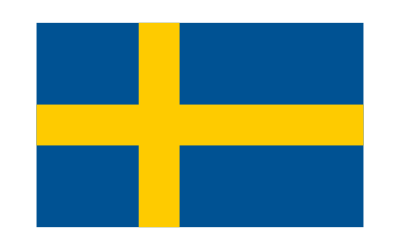
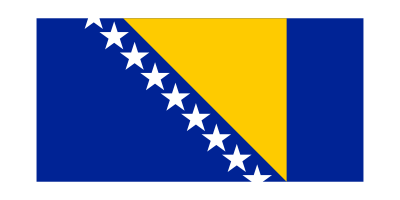
| Expected output: |  
  | {-Graphics-,-Graphics-,-Graphics-} |

Haga un grafo de los 2 colores que sean vecinos más cercanos a cada uno de los colores en Table[Hue[h],{h,0,1,.05}]. »

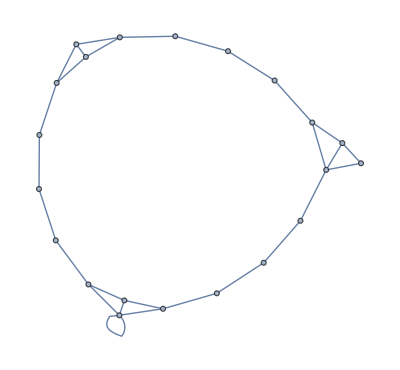
| Expected output: |  
  | -Graphics- |

Genere una lista de 100 números aleatorios entre 0 y 100, y hacer un grafo de los dos vecinos más próximos para cada uno. »

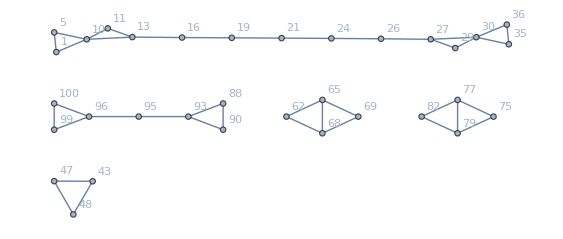
| Sample expected output: |  
  | -Graphics- |

Acomode las banderas de Asia en cúmulos de banderas similares. »

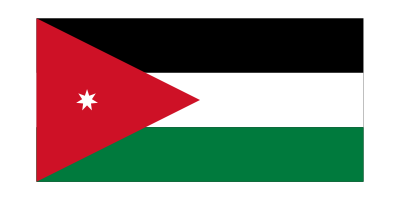
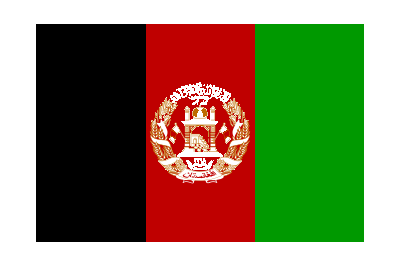
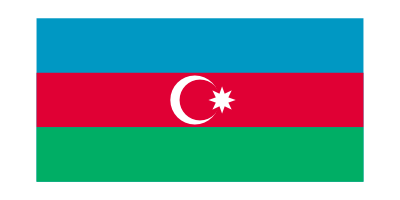
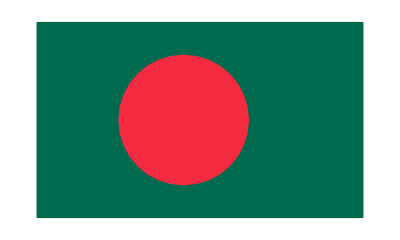
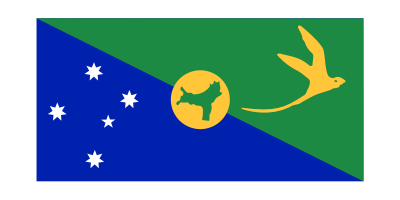
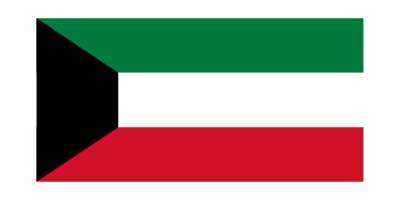
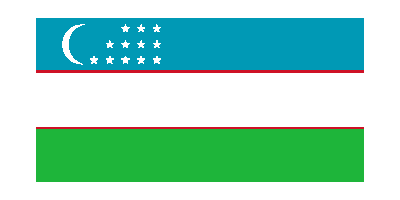
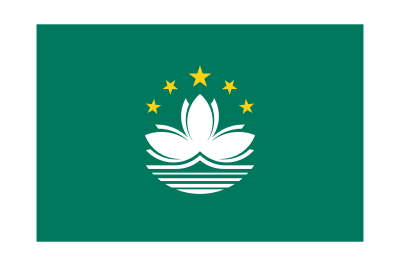

| Expected output: |  
  | {{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}} |

Produzca imágenes rasterizadas de las letras del alfabeto inglés en tamaño 20, y luego haga un grafo de los 2 vecinos más próximos para cada uno. »

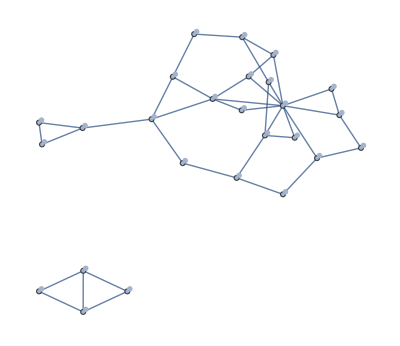
| Expected output: |  
  | -Graphics- |

Genere una tabla con los resultados de usar TextRecognize en “hello”, rasterizado en tamaño 50 y con niveles de difuminación entre 1 y 10. »

| Expected output: |  
  | {"hello","hello","hello","hello","hello","hello","hllo","","",""} |

Haga un dendrograma con las imágenes de las primeras 10 letras del alfabeto. »

| Expected output: |  
  | -Graphics- |

Haga una imagen del espacio de características de las letras mayúsculas del alfabeto inglés. »

| Expected output: |  
  | -Graphics- |

Construya una tabla de identificaciones de imagen para una foto de la torre Eiffel, con borrosidades del 1 al 5. »

| Expected output: |  
  | {"Eiffel Tower","tower","tower","tower","device"} |

Clasifique el sentimiento del artículo “happiness” en Wikipedia. »

| Expected output: |  
  | "Neutral" |

De los colores en la lista Table[Hue[h],{h,0,1,.05}], encuentre los 3 más cercanos al Pink. »

| Expected output: |  
  | {Hue[0.9500000000000001],Hue[0.9],Hue[0.05]} |

Obtenga todas las fracciones i/j para i y j hasta 500, y encontrar las 10 más cercanas a pi. »

| Expected output: |  
  | {355/113,377/120,333/106,399/127,311/99,421/134,443/141,289/92,465/148,487/155} |

Genere una lista de 10 números aleatorios del 0 al 10, y hacer un grafo de los 3 vecinos más próximos para cada uno. »

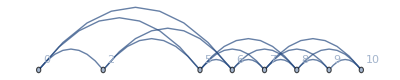
| Expected output: |  
  | -Graphics- |

Encuentre cúmulos de colores similares en una lista de 100 colores aleatorios. »

| Expected output: |  
  | {{RGBColor[0.8116438051434329, 0.8547919864863347, 0.7807710853793401],RGBColor[0.2983278570382957, 0.9907444932950316, 0.9284043344039434],RGBColor[0.18676117011450066, 0.5486089602170863, 0.04303247680226141],RGBColor[0.4044608902823441, 0.9788998961090443, 0.8108975624714536],RGBColor[0.5308001574813235, 0.9503472359039511, 0.8646083755834806],RGBColor[0.5926608241659339, 0.4671421812435703, 0.027570072930602985],RGBColor[0.49843743964638865, 0.7588128836239783, 0.6588996785867525],RGBColor[0.6788691428209239, 0.8865118691450595, 0.06859340947663295],RGBColor[0.3966954095359472, 0.9303983446364068, 0.27133513969525125],RGBColor[0.7496777159050012, 0.8414031368083361, 0.29000881481349006],RGBColor[0.1722869702422274, 0.42066881136044554, 0.18877704427888808],RGBColor[0.020568097401979735, 0.32843933224376776, 0.2578912775452169],RGBColor[0.4276762158276948, 0.9445301871184215, 0.6339408432442302],RGBColor[0.3449333805776824, 0.8214093187031501, 0.00535396147946221],RGBColor[0.9595114792486563, 0.9614567195621035, 0.09956803288245264],RGBColor[0.13927723404143122, 0.9837658758454813, 0.6275322853052734],RGBColor[0.4129872979782936, 0.599123151026224, 0.5563798982651478],RGBColor[0.5517409716001453, 0.7226268672047083, 0.04296745155978088],RGBColor[0.2471012449687613, 0.6622219052252245, 0.34136700529740893],RGBColor[0.00852878273374924, 0.7623891609381206, 0.495048201930645],RGBColor[0.410530117230961, 0.65951899493187, 0.31274019237510875],RGBColor[0.14914425266109754, 0.8632288046219025, 0.2165769996518021],RGBColor[0.5019554020533212, 0.5771425709059108, 0.4324648041012522],RGBColor[0.2375846642639532, 0.7953276430316651, 0.9346352336682711],RGBColor[0.5670638896981823, 0.30694748662903737, 0.07724772234151844],RGBColor[0.9836330486106633, 0.9337141420685637, 0.45110780147188234],RGBColor[0.548151102001315, 0.9273818734933321, 0.6138604019189067],RGBColor[0.08996343949980967, 0.7502285322367264, 0.7647837622874905],RGBColor[0.9554445238224603, 0.9118174885785313, 0.7586039763217882],RGBColor[0.12407876246761118, 0.8951986963374581, 0.405054951518828],RGBColor[0.3518853673765441, 0.6267881822227646, 0.01601455063963053],RGBColor[0.38175543134617906, 0.6109792496345561, 0.30321055377645356],RGBColor[0.5015968883258048, 0.9477341972992892, 0.7518749706067847],RGBColor[0.4853791041906068, 0.9983056811536988, 0.059586297674913524],RGBColor[0.39598681356054666, 0.5894657294683947, 0.2897133293523855],RGBColor[0.06510008212093177, 0.7580810151353965, 0.4838966525370989],RGBColor[0.02229677965825383, 0.35028891391213257, 0.0684550207396537],RGBColor[0.15578960479774717, 0.33156505911261824, 0.10795082362400787],RGBColor[0.9666406011133539, 0.6653552686335491, 0.5546554666254075],RGBColor[0.21832422216206182, 0.4452088456726624, 0.34195667187604584],RGBColor[0.4939446101923697, 0.31678858836269796, 0.11346988660388835],RGBColor[0.9566388456878347, 0.9651195544633302, 0.9076564789046491],RGBColor[0.4000855073593619, 0.39588066174906866, 0.1685452332949151],RGBColor[0.5700736595139675, 0.4069545472059297, 0.1981313907220874],RGBColor[0.16637070232988593, 0.6273450506223697, 0.6129198387249786],RGBColor[0.15217789308335927, 0.6805446503579162, 0.7536712821543405],RGBColor[0.011500166973726689, 0.9344737120630893, 0.41519231703372195],RGBColor[0.6487763190386047, 0.9218976224198998, 0.711816672844579],RGBColor[0.47327935747334204, 0.8834140175937308, 0.33245673464773584],RGBColor[0.25560515056407795, 0.8012401319897553, 0.15094027368448049],RGBColor[0.13360546814982577, 0.7871863239201633, 0.018599162734135977],RGBColor[0.38337417819768205, 0.4988952587556723, 0.08321860516969015],RGBColor[0.4181367040733106, 0.49313383402211364, 0.10167945128775124],RGBColor[0.4812053533680498, 0.873332380181423, 0.327028956990717],RGBColor[0.5269434582467774, 0.8294337802982428, 0.1734709900484559]},{RGBColor[0.37266534273681007, 0.38750269832660855, 0.3948182017762212],RGBColor[0.733606571264461, 0.4291909747287308, 0.4301886698173236],RGBColor[0.17707863410973768, 0.672607405954065, 0.8338273497920801],RGBColor[0.8745580077995285, 0.08910005366925322, 0.5820198361552016],RGBColor[0.9090294322469556, 0.2839329014344203, 0.5231271919589293],RGBColor[0.4864384781423896, 0.2590016473319656, 0.8939198034327294],RGBColor[0.2674220618976657, 0.5345197867819858, 0.7888815584252213],RGBColor[0.18736123677107708, 0.3952086052502788, 0.86460527303447],RGBColor[0.7776461280660796, 0.8643601244579295, 0.9944319426310919],RGBColor[0.10244743490058794, 0.1869170597224914, 0.6271170684614624],RGBColor[0.4573447796522936, 0.007181376876192136, 0.566195028583903],RGBColor[0.23258722219837846, 0.08344742427005825, 0.30644177688225716],RGBColor[0.711485166849398, 0.017375777675906035, 0.7454946682315056],RGBColor[0.31452599923983104, 0.6908103742720597, 0.9463506847311731],RGBColor[0.922559309792595, 0.2703946335791436, 0.09665543181913394],RGBColor[0.11122524183982829, 0.12772449779541217, 0.6139200516853858],RGBColor[0.6357194627252103, 0.15357943517679362, 0.860476954867391],RGBColor[0.4431832834876257, 0.18321465791748515, 0.7764518003586576],RGBColor[0.3553518860908462, 0.6443320866741731, 0.7499636864238166],RGBColor[0.8943854155561495, 0.03560200287351467, 0.16578917868909593],RGBColor[0.6672396717157738, 0.3586192991395154, 0.8976595916455246],RGBColor[0.37001635641206, 0.3047563933568622, 0.7684408201506054],RGBColor[0.38698691150966935, 0.10328204902950966, 0.8013210231747274],RGBColor[0.29215345853340424, 0.35497646703617836, 0.6346432521789236],RGBColor[0.9678407581110904, 0.025426491397912976, 0.587777889276665],RGBColor[0.4918965330955356, 0.29233426982370303, 0.5281824844462943],RGBColor[0.1252423737911874, 0.5183189386335805, 0.7491160058315705],RGBColor[0.9765556387211944, 0.12357617097291551, 0.5068373458296718],RGBColor[0.8227934753153485, 0.3797246867796864, 0.6782582898466567],RGBColor[0.6820734720667967, 0.43856527685111324, 0.8695673460178908],RGBColor[0.11654903299881392, 0.07006336344132391, 0.56484752468554],RGBColor[0.6402988781363921, 0.035330434441392944, 0.28001275709114415],RGBColor[0.4249737173056105, 0.08087713350797054, 0.5561568741925262],RGBColor[0.7495302686726302, 0.3453338459340154, 0.3119406215616949],RGBColor[0.836090631447431, 0.10393312541533217, 0.9133348768403533],RGBColor[0.19151655035273674, 0.14390156161230028, 0.5247101500257152],RGBColor[0.8789399682999111, 0.042929493135203334, 0.19233219566452364],RGBColor[0.8279081820793655, 0.007601665021679249, 0.007776314948584773],RGBColor[0.8905220469868362, 0.6720465313460078, 0.8782899541874138],RGBColor[0.4739838883353795, 0.01643240988333261, 0.7672816104627056],RGBColor[0.73262590528079, 0.4345872718612065, 0.9513218213654053],RGBColor[0.7193138046226939, 0.736637476380962, 0.9909551197977506],RGBColor[0.5532261835871646, 0.1424067735626049, 0.6840947116434117],RGBColor[0.24015696649735507, 0.2276921291555416, 0.5618669828113934],RGBColor[0.3614530023699991, 0.23838000474075272, 0.351099450461986]}} |

Haga una imagen del espacio de características para las letras mayúsculas y minúsculas del alfabeto inglés. »

| Expected output: |  
  | -Graphics- |

Preguntas y respuestas

¿Cómo es posible que se obtengan resultados diferentes de los mostrados aquí?

Probablemente, porque las funciones para aprendizaje de máquinas en Wolfram Language cada vez tienen más entrenamiento, lo que hace que los resultados vayan cambiando, y se esperaría que fueran cada vez mejores. En el caso de TextRecognize, los resultados pueden depender del detalle de las fuentes utilizadas y de qué manera se generaron y rasterizaron en la computadora que se esté usando.

¿Cómo funciona internamente ImageIdentify?

Se basa en redes neuronales artificiales inspiradas en la forma como parece funcionar el cerebro. Se le ha entrenado con millones de ejemplos de imágenes, con lo cual ha ido aprendiendo progresivamente a hacer distinciones. Y, de manera parecida al juego de “veinte preguntas”, a base de usar suficientes distinciones puede determinar a qué corresponde una imagen.

¿Cuántas clases de cosas puede reconocer ImageIdentify?

Por lo menos 10 000, que es más de lo que puede hacer una persona típica. (En inglés hay alrededor de 5 000 nombres “representables como imagen”.)

¿Qué puede causar que ImageIdentify proporcione una respuesta equivocada?

Una causa frecuente es que se le pregunte algo que no se parezca a nada para lo que haya recibido entrenamiento. Esto puede pasar si algún objeto se encuentra en una configuración o ambiente poco habitual (por ejemplo, si una embarcación no tiene un trasfondo azulado). ImageIdentify intenta generalmente encontrar algún tipo de coincidencia, y muchas veces los errores que comete son parecidos a los “errores humanos”.

¿Se pueden pedir las probabilidades que ImageIdentify asigna a diferentes identificaciones?

Sí. Por ejemplo, para conocer las probabilidades de las primeras 10 identificaciones en todas las categorías, se usa ImageIdentify[image,All,10,"Probability"].

Típicamente, ¿cuántos ejemplos necesitaría Classify para trabajar bien?

Si se trata de un área general que conozca bien (imágenes cotidianas), podrían bastar unas cien. Pero en áreas nuevas, podrían requerirse millones de ejemplos para alcanzar buenos resultados.

¿Cómo determina Nearest la distancia entre colores?

Usa la función ColorDistance, que está basada en un modelo de la visión de colores humana.

¿Cómo determina Nearest las palabras cercanas?

Buscando aquellas con la menor EditDistance, esto es, la que requiere menor número de inserciones, eliminaciones y sustituciones de letras individuales.

¿Puede un mismo grafo tener una o varias partes no conectadas?

Absolutamente. El último grafo de esta sección es un ejemplo de eso.

¿Qué características usa FeatureSpacePlot?

No hay una respuesta sencilla para esta pregunta. Cuando se le presenta una colección de objetos, aprende sus características distintivas; si bien, típicamente, parte de haber visto muchos otros objetos del mismo tipo general (como imágenes).

Notas técnicas

Wolfram Language almacena en la nube sus más recientes clasificadores para aprendizaje de máquinas, pero en el caso de que se use un sistema de escritorio, se descargarán automáticamente y correrán localmente.

BarcodeImage y BarcodeRecognize trabajan con códigos de barras y códigos QR en vez de texto puro.

ImageIdentify es el núcleo de lo que hace el sitio web imageidentify.com.

Si solo se dan a Classify ejemplos para entrenamiento, producirá una ClassifierFunction que se puede aplicar posteriormente a muchos tipos de datos diferentes. Es así como casi siempre se usa Classify en la práctica.

Puede obtenerse un conjunto estándar amplio para entrenamiento con dígitos manuscritos usando ResourceData["MNIST"].

Classify elige automáticamente entre métodos tales como regresión logística, Bayes ingenuo, bosques aleatorios y máquinas de vectores de soporte, así como redes neuronales.

FindClusters realiza aprendizaje automático no supervisado, en el que la computadora simplemente revisa los datos sin que se le dé información al respecto. Classify realiza aprendizaje automático supervisado, dado un conjunto de ejemplos de entrenamiento.

Dendrogram lleva a cabo una formación jerárquica de cúmulos, y puede usarse para reconstruir árboles evolucionarios en áreas como la bioinformática y la lingüística histórica.

FeatureSpacePlot hace reducción de dimensión, partiendo de datos representados por muchos parámetros, y encontrando alguna buena manera de “proyectarlos” para poder obtener imágenes en 2D.

Rasterize/@Alphabet[ ] es una mejor forma de rasterizar letras, pero /@ no será tratado hasta la Sección 25.

FeatureExtraction permite obtener los vectores de características utilizados por FeatureSpacePlot.

FeatureNearest es como Nearest, excepto que aprende lo que debe considerarse como próximo, examinando los datos mismos que se le den. Esto es lo que se requiere para construir algo como una función de búsqueda de imágenes.

Uno puede construir y entrenar sus propias redes neuronales en Wolfram Language mediante el uso de funciones como NetChain, NetGraph y NetTrain. NetModel da el acceso a redes preconstruidas.

Para explorar más

Guía para aprendizaje de máquinas en Wolfram Language »